# Лабораторная работа №8

Выполнила студентка ММФ БГУ
1 к 5 гр Бельская Е.А.
  3.11 .2019

## Задание 2.1

```mathematica
kmPoint[km,id_String,coord:{_,_}]
```

kmPoint[km,id_String,coord:{_,_}]

## Задание 2.2-2.3

Конструктор–оператор kmPoint, который по указанным
декартовым координатам точки строит ее представление.

```mathematica
ClearAll[kmPoint]
```

```mathematica
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord]
```

```mathematica
kmPoint[{1,2}]
```

kmPoint[km,,{1,2}]

## Задание 2.4

Определим конструктор, позволяющий задавать точку указанием ее
имени и координат.

```mathematica
kmPoint[id_String,coord:{_,_}]:=kmPoint[km, id,coord]
```

```mathematica
kmPoint["A",{1,2}]
```

kmPoint[km,A,{1,2}]

```mathematica
myP=kmPoint["Моя точка",{1,0}]
```

kmPoint[km,Моя точка,{1,0}]

## Задание 2.5 - 2.6

Создайте возможность задания объекта точка на плоскости
посредством указания ее полярных координат (согласованных с прямоугольной декартовой системой координат).

```mathematica
kmPoint[{ϕ_,r_},"pol"]:=kmPoint[km,"",{r*Cos[ϕ],r*Sin[ϕ]} ]
```

```mathematica
kmPoint[{π/3,2},"pol"]
```

kmPoint[km,,{1,√3}]

```mathematica
kmPoint[id_String,{ϕ_,r_},"pol"]:=kmPoint[km,id,{r*Cos[ϕ],r*Sin[ϕ]}]
kmPoint["A",{π/3,2},"pol"]
```

kmPoint[km,A,{1,√3}]

## Задание 2.7

Напишите оператор, возвращающий имя объекта точка, если оно
существует.

```mathematica
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint["A",{1,2}]["id"]
```

A

```mathematica
myP["id"]
```

Моя точка

```mathematica
kmPoint[{5,2}]["id"]
```

Точка

```mathematica
kmPoint[{π/3,2},"pol"]["id"]
```

Точка

## Задание 2.8

Напишите оператор, возвращающий декартовы координаты заданного
объекта точка на плоскости.

```mathematica
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
```

```mathematica
kmPoint[{π/3,2},"pol"]["coord"]
```

{1,√3}

```mathematica
myP["coord"]
```

{1,0}

## Задание 2.9-10

Постройте булеву функцию, позволяющую определить, имеет ли
представленный объект точка на плоскости имя.

```mathematica
NamedQ[kmPoint[km,id_String,___]]^:=id≠""
```

```mathematica
NamedQ[myP]
```

True

```mathematica
?kmPoint
```

Global`kmPoint

kmPoint[km,id_String,___][id]:=If[id==,Точка,id]
 
NamedQ[kmPoint[km,id_String,___]]^:=id≠
 
kmPoint[coord:{_,_}]:=kmPoint[km,,coord]
 
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord]
 
kmPoint[{ϕ_,r_},pol]:=kmPoint[km,,{r Cos[ϕ],r Sin[ϕ]}]
 
kmPoint[id_String,{ϕ_,r_},pol]:=kmPoint[km,id,{r Cos[ϕ],r Sin[ϕ]}]

```mathematica
NamedQ[kmPoint[{π/3,2},"pol"]]
```

False

```mathematica
{DownValues[kmPoint],UpValues[kmPoint],SubValues[kmPoint]}
```

{{HoldPattern[kmPoint[coord:{_,_}]]:>kmPoint[km,,coord],HoldPattern[kmPoint[id_String,coord:{_,_}]]:>kmPoint[km,id,coord],HoldPattern[kmPoint[{ϕ_,r_},pol]]:>kmPoint[km,,{r Cos[ϕ],r Sin[ϕ]}],HoldPattern[kmPoint[id_String,{ϕ_,r_},pol]]:>kmPoint[km,id,{r Cos[ϕ],r Sin[ϕ]}]},{HoldPattern[NamedQ[kmPoint[km,id_String,___]]]:>id≠},{HoldPattern[kmPoint[km,id_String,___][id]]:>If[id==,Точка,id],HoldPattern[kmPoint[km,id_String,___,coord_List,___][coord]]:>coord}}

## Задание 2.11

Три точки P1, P2, P3, заданные в прямоугольной декартовой системе
координат соответственно координатами (−1, 0), (5, 3), (−2, 2).Представьте точки P1, P2, P3  в Mathematica, каждую как экземпляр
объекта «точка на плоскости», и отобразите представленные точки в
графической области.

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

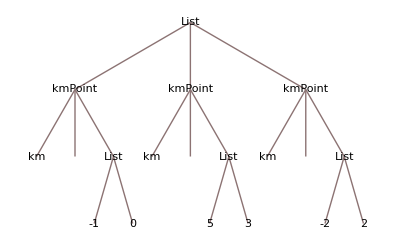

```mathematica
{P1,P2,P3}//TreeForm
```

```mathematica
#["coord"]&/@{P1,P2,P3}
```

{{-1,0},{5,3},{-2,2}}

```mathematica
Point[#["coord"]&/@{P1,P2,P3}]
```

Point[{{-1,0},{5,3},{-2,2}}]

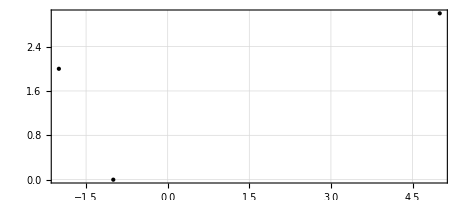

```mathematica
Graphics[Point/@(#["coord"]&/@{P1,P2,P3}),Frame->True, GridLines->Automatic]
```

```mathematica
ClearAll[kmGraphics2D];
kmGraphics2D[points_List,opts___]:=Graphics[Point/@(#["coord"]&/@points),opts];
```

```mathematica
kmGraphics2D[{ P1,P2, P3},Frame->True,GridLines->Automatic]
```

-Graphics-

## Задание 2.12

2.12 Координаты точки M в полярной системе координат равны (5 π/4, 1).a) Представьте точку М в Mathematica, используя конструктор объекта
      точка на плоскости.b) Получите декартовы координаты точки М при условии, что начала
    координат совпадают, а полярная ось совпадает с положительной
    частью оси абсцисс.c) Получите имя точки.d) В графической области изобразите точку М зеленым цветом.

```mathematica
M=kmPoint["M",{(5π)/4,1},"pol"]
```

kmPoint[km,M,{-1/(√2),-1/(√2)}]

```mathematica
M["id"]
```

M

```mathematica
M["coord"]
```

{-1/(√2),-1/(√2)}

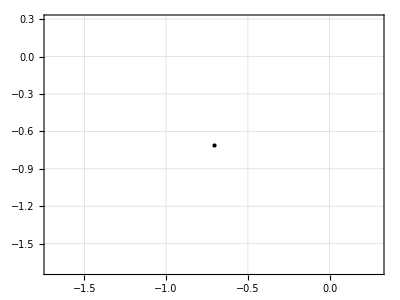

```mathematica
kmGraphics2D[{M},BaseStyle->{Green,PointSize[0.03]}, Frame->True,GridLines->Automatic]
```

## Задание 2.13

Найдите расстояние между точками M и N, имеющими полярные
координаты M (π/4, 3) и N (3 π/4, 4).В графической области отобразите
точку M красным цветом, точку N–синим, отрезок, их соединяющий–серым; при этом точку, расположенную дальше от полярной оси, отобразите большей по размеру, а также подпишите длину отрезка.

```mathematica
Mp=kmPoint["M",{π/4,3},"pol"]
```

kmPoint[km,M,{3/(√2),3/(√2)}]

```mathematica
Np=kmPoint["N",{(3π)/4,4},"pol"]
```

kmPoint[km,N,{-2 √2,2 √2}]

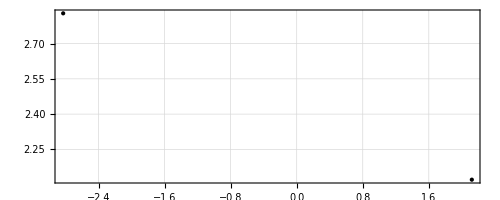

```mathematica
kmGraphics2D[{Mp,Np}, Frame->True,GridLines->Automatic]
```

```mathematica
{Mp,Np}/.P_kmPoint:>Point[P["coord"]]
```

{Point[{3/(√2),3/(√2)}],Point[{-2 √2,2 √2}]}

```mathematica
dist[P1:{x1_, y1_}, P2:{x2_, y2_}]:=√((P1-P2).(P1-P2)) //Simplify
```

```mathematica
dist[Mp["coord"],Np["coord"]]
```

5

```mathematica
TextDist[m_List,n_List]:= (m+n)*0.51
```

```mathematica
ClearAll[kmPointGr];
kmPointGr[points_List,opts___]:=Graphics[points/.P_kmPoint:>Tooltip[Point[P["coord"]],Row@{P["id"],"(",Row[P["coord"],","],")"}],opts];
```

```mathematica
check[m_List,n_List]:=If[m[[2]]>n[[2]],PointSize[0.03],PointSize[0.01]]
```

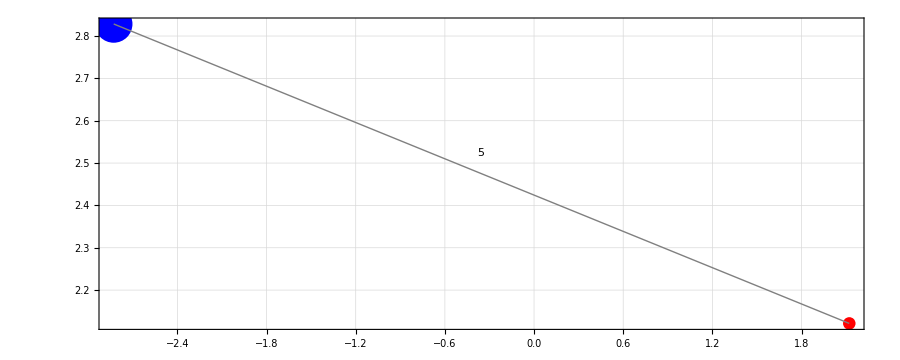

```mathematica
kmPointGr[{Red,check[Mp["coord"],Np["coord"]],Mp,Blue,check[Np["coord"],Mp["coord"]],Np,Gray,Line[{Mp["coord"],Np["coord"]}],Style[Text[dist[Mp["coord"],Np["coord"]],TextDist[Mp["coord"],Np["coord"]]],Black,Large]},Frame->True,GridLines->Automatic,ImageSize->900]
```

## Задание 2.14

Напишите функцию, которая вычисляет координаты точки, делящей
отрезок, заданный координатами своих концов, в отношении λ.

```mathematica
coordFind[first_List,second_List,λ_]:=(first*1+second*λ)/(1+λ)//Simplify
```

```mathematica
coordFind[{0,0},{1,0},1/2]
```

{1/3,0}

## Задание 2.15

Дан треугольник А (0, 0), В (4, -3), С (12, 5).Вычислите координаты
точки D пересечения биссектрисы внутреннего угла A с противолежащей
стороной BC.Используйте свойство биссектрисы : точка D делит сторону
BC в отношении λ = (длина АС)/(длина АВ).

```mathematica
Ap=kmPoint["A",{0,0}]
```

kmPoint[km,A,{0,0}]

```mathematica
Bp=kmPoint["B",{4,-3}]
```

kmPoint[km,B,{4,-3}]

```mathematica
Cp=kmPoint["C",{12,5}]
```

kmPoint[km,C,{12,5}]

```mathematica
AC=dist[Ap["coord"],Cp["coord"]]
```

13

```mathematica
AB=dist[Ap["coord"],Bp["coord"]]
```

5

```mathematica
rel=AC/AB
```

13/5

```mathematica
coordFind[Bp["coord"],Cp["coord"],rel]
```

{88/9,25/9}

## Задание 2.16

Вычислите полярные координаты вершин правильного
шестиугольника, вписанного в окружность заданного радиуса.Расположите полюс в точке О, являющейся центром шестиугольника, а
одну из вершин шестиугольника–на полярной оси при нулевом угле ее
поворота.Изобразите вычисленные вершины, шестиугольник, описанную
окружность.Напишите функцию, вычисляющую декартовы координаты
вершин правильного n - угольника, вписанного в окружность заданного
радиуса.Используйте метод построения вершин полигона в полярных
4
координатах.Изобразите вычисленные вершины, полигон, описанную
окружность.

```mathematica
myfunc[n_,r_]:=kmPoint[{#,r},"pol"]["coord"]&/@Range[0,2π,(2π)/n]
```

```mathematica
p=myfunc[6,6]
```

{{6,0},{3,3 √3},{-3,3 √3},{-6,0},{-3,-3 √3},{3,-3 √3},{6,0}}

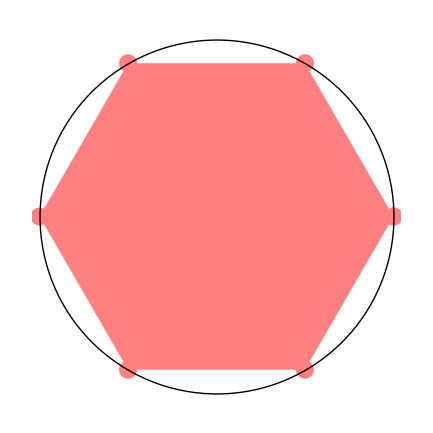

```mathematica
Show[kmPointGr[{PointSize[0.03],Pink,kmPoint/@p}],Graphics[{Pink,Polygon[p]}],Graphics[Circle[{0,0},6]]]
```